```mathematica
r1=y^2+(x-1)^2;
r2=y^2+(x+1)^2;
```

```mathematica
2r1-(r1-2)^2-(r2-2)^2//Simplify
```

```mathematica
expresion[x_,y_]:=-2 (2 x+x^2+x^4-3 y^2+2 x^2 y^2+y^4);
Sx[x_,y_]:=(2x)((1+x^2+y^2)/((x^2+(y+1)^2)(x^2+(y-1)^2)));
Sy[x_,y_]:=(2y)((1-x^2-y^2)/((x^2+(y+1)^2)(x^2+(y-1)^2)));
```

```mathematica
Solve[expresion[x,y]==0,y]
```

{{y→-(√(3-2 x^2-√(9-8 x-16 x^2)))/(√2)},{y→(√(3-2 x^2-√(9-8 x-16 x^2)))/(√2)},{y→-(√(3-2 x^2+√(9-8 x-16 x^2)))/(√2)},{y→(√(3-2 x^2+√(9-8 x-16 x^2)))/(√2)}}

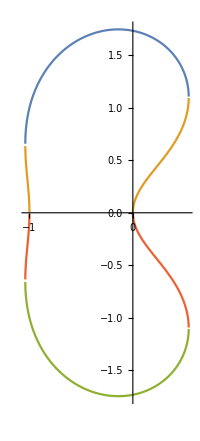

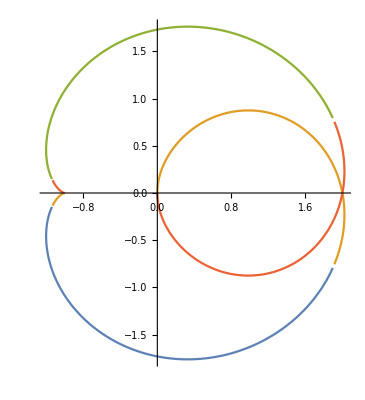

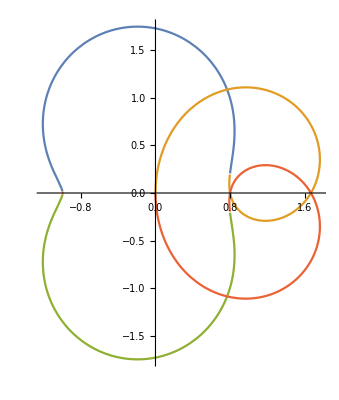

```mathematica
expresion1[x_]:=(√(3-2 x^2+√(9-8 x-16 x^2)))/(√2)
expresion2[x_]:=(√(3-2 x^2-√(9-8 x-16 x^2)))/(√2)
conjunto=ParametricPlot[{{x,expresion1[x]},{x,expresion2[x]},{x,-expresion1[x]},{x,-expresion2[x]}},{x,-2,2}];
conjuntoImagen=ParametricPlot[{{Sx[x,expresion1[x]],Sy[x,expresion1[x]]},{Sx[x,expresion2[x]],Sy[x,expresion2[x]]},{Sx[x,-expresion1[x]],Sy[x,-expresion1[x]]},{Sx[x,-expresion2[x]],Sy[x,-expresion2[x]]}},{x,-2,2}];
conjuntoImagenImagen=ParametricPlot[{{Sx[Sx[x,expresion1[x]],Sy[x,expresion1[x]]],Sy[Sx[x,expresion1[x]],Sy[x,expresion1[x]]]},{Sx[Sx[x,expresion2[x]],Sy[x,expresion2[x]]],Sy[Sx[x,expresion2[x]],Sy[x,expresion2[x]]]},{Sx[Sx[x,-expresion1[x]],Sy[x,-expresion1[x]]],Sy[Sx[x,-expresion1[x]],Sy[x,-expresion1[x]]]},{Sx[Sx[x,-expresion2[x]],Sy[x,-expresion2[x]]],Sy[Sx[x,-expresion2[x]],Sy[x,-expresion2[x]]]}},{x,-2,2}];
Show[conjunto]
Show[conjuntoImagen]
Show[conjuntoImagenImagen]
```

```mathematica
Búsqueda de los puntos de corte con la recta vertical 1/2
```

```mathematica
Solve[expresion[1/2,y]==0,y]
```

{{y→-(√3)/2},{y→(√3)/2},{y→-(√7)/2},{y→(√7)/2}}

```mathematica
Punto1=Graphics[{PointSize[Large],Green,Point[{1/2,-(√3)/2}]}];
Punto2=Graphics[{PointSize[Large],Blue,Point[{1/2,(√3)/2}]}];
Punto3=Graphics[{PointSize[Large],Red,Point[{1/2,-(√7)/2}]}];
Punto4=Graphics[{PointSize[Large],Orange,Point[{1/2,(√7)/2}]}];
```

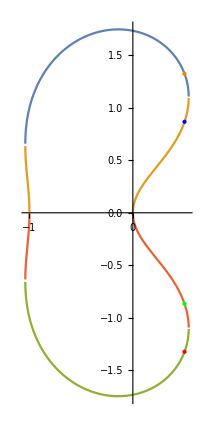

```mathematica
Show[conjunto,Punto1,Punto2,Punto3,Punto4]
```

```mathematica
Punto5=Graphics[{PointSize[Large],Green,Point[{Sx[1/2,-(√3)/2],Sy[1/2,-(√3)/2]}]}];
Punto6=Graphics[{PointSize[Large],Blue,Point[{Sx[1/2,(√3)/2],Sy[1/2,(√3)/2]}]}];
Punto7=Graphics[{PointSize[Large],Red,Point[{Sx[1/2,-(√7)/2],Sy[1/2,-(√7)/2]}]}];
Punto8=Graphics[{PointSize[Large],Orange,Point[{Sx[1/2,(√7)/2],Sy[1/2,(√7)/2]}]}];
```

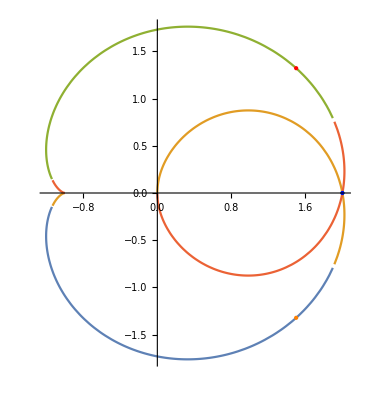

```mathematica
Show[conjuntoImagen,Punto5,Punto6,Punto7,Punto8]
```

```mathematica
¿Y si tomamos una circunferencia que solo pase 1 vez por el 0?
```

```mathematica
Nf[z_]:=(1/2)(z+(1/z))
```

```mathematica
circ[a_]:=E^(I*a)+1
```

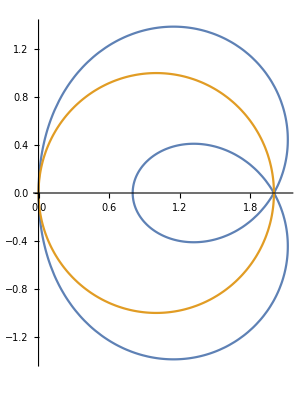

```mathematica
ParametricPlot[{ReIm[1/Nf[circ[a]]],ReIm[circ[a]]},{a,0,2Pi}]
```

```mathematica
Sf[z_]:=1/Nf[z]
circ1[a_]:=0.05*E^(I*a)+1
```

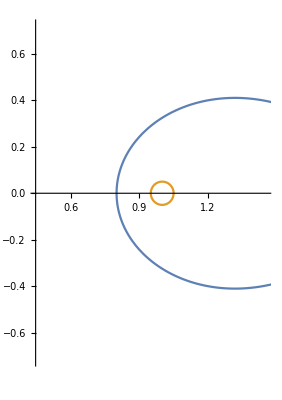

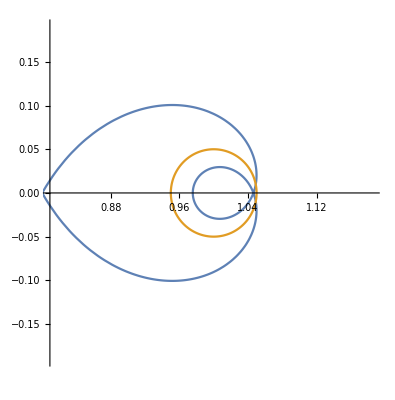

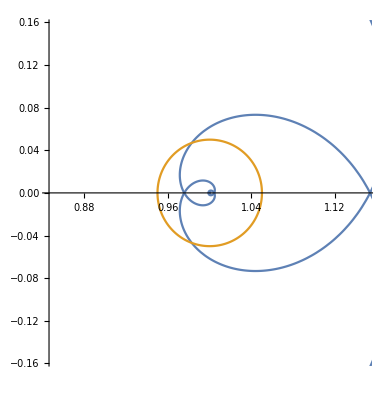

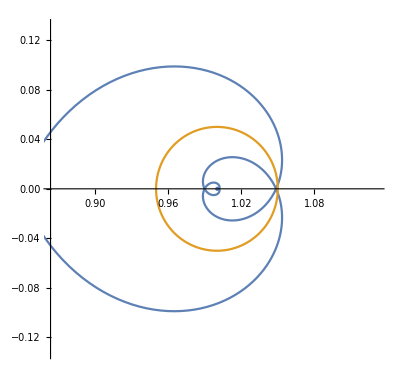

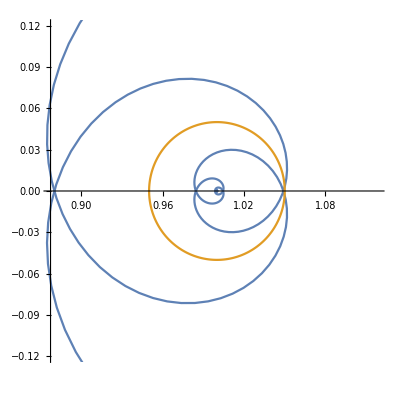

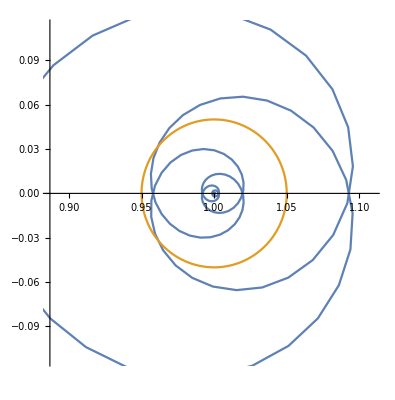

```mathematica
For[i=0;t[x_]:=Nest[Sf,circ[x],i];
h[x_]:=Nest[Nf,circ[x],i-1],i<6,i++;

grafico=ParametricPlot[{ReIm[t[x]],ReIm[circ1[x]]},{x,0,2Pi}];
Print[Show[{grafico}]]]
```